```mathematica
(*This controls the base color*)
s = .6;
CollorCorrelatedWithBrightnessAvg[l_]:=Module[{L},
If[l==0,L=.99-RandomReal[]/10,L=l];
Hue[
{s+L*Random[]/4,
(1-L),
L}]]
(*Choose one of the above colormaps*)
colorMap = CollorCorrelatedWithBrightnessAvg;
```

```mathematica
{w,h}={240,180}
boudryCorners = {{0,0},{w,0},{0,h},{w,h}};
```

{240,180}

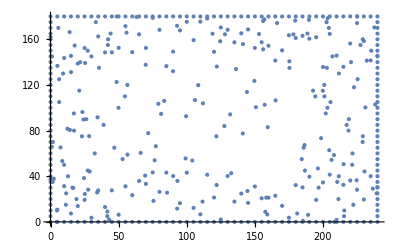

```mathematica
verts = {};
verts = verts∪boudryCorners;
verts = verts∪Table[{RandomReal[{0,w}],RandomReal[{0,h}]},{idx,0,100}];
verts = verts∪Table[{idx,0},{idx,0,w,5}];
verts = verts∪Table[{idx,h},{idx,0,w,5}];
verts = verts∪Table[{0,idx},{idx,0,h,5}];
verts = verts∪Table[{w,idx},{idx,0,h,5}];
div = 4;
verts = verts∪Table[{idx,RandomReal[h/div]},{idx,0,w,5}];
verts = verts∪Table[{idx,h-RandomReal[h/div]},{idx,0,w,5}];
verts = verts∪Table[{RandomReal[w/div],idx},{idx,0,h,5}];
verts = verts∪Table[{w-RandomReal[w/div],idx},{idx,0,h,5}];
ListPlot[verts]
```

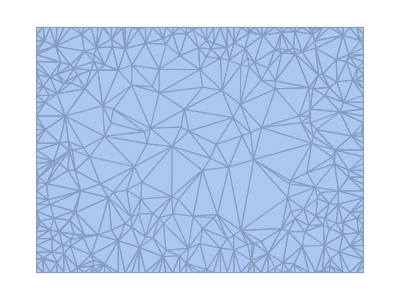

```mathematica
imageMesh=DelaunayMesh[verts]
```

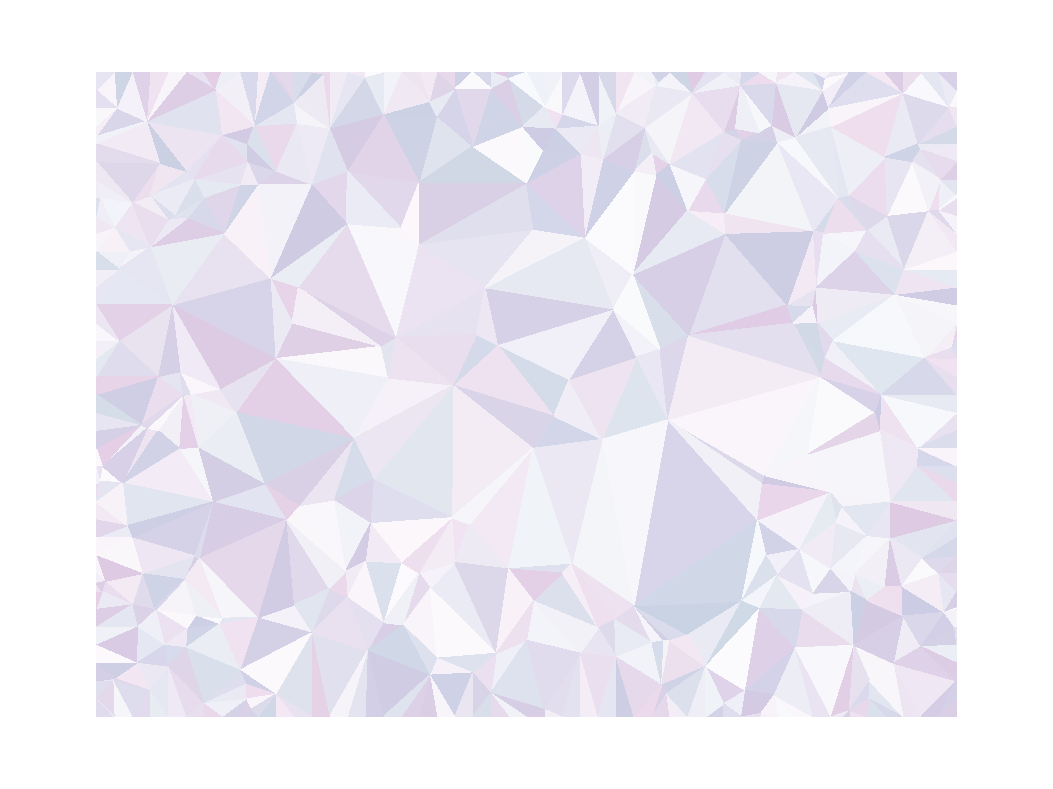

```mathematica
res = Graphics[Table[{colorMap[0],p},{p,MeshPrimitives[imageMesh,2]}]]
```